# CForm for Bessel Beams

Yoonkyung Eunnie Lee
2015.04.16

This version outputs L, M, N as a function of (L,x,y,z)

Note

M corresponds to a "Transverse" Field where Longitudinal component is zero, when a=[0,0,1]. 
E=∑M_PL(H=∑N_PL)  corresponds to TE mode, also called Azimuthal Polarization 
H=∑M_PL(E=∑N_PL)  corresponds to TM mode also called Radial Polarization 

Azimuthal Pol: best represented by Re(M)
Radial Pol: best represented by Im(N)

## Initialize

```mathematica
ClearAll["Global`*"];
t0=AbsoluteTime[];
$ProcessorCount
ParallelEvaluate[$ProcessID]

SetDirectory[NotebookDirectory[]];

line=4;
point=4;
(**)
tickthickness = 1.25;
fontstyle = {12, FontFamily -> "Helvetica"};
(**)
SetOptions[Plot, 
	ImageSize -> Large,
	LabelStyle -> fontstyle,
	Frame -> True,
	FrameTicksStyle -> AbsoluteThickness[tickthickness],
	AspectRatio -> 1,
	Axes -> False
];
(**)
SetOptions[VectorPlot, 
	ImageSize -> Medium,
	LabelStyle -> fontstyle,
	Frame -> True,
	FrameTicksStyle -> AbsoluteThickness[tickthickness],
     VectorPoints->20,VectorScale->{0.1,Scaled[0.9]},
	Axes -> False
];
(**)
SetOptions[ListPlot,
	ImageSize -> Medium,
	LabelStyle -> fontstyle,
	Frame -> True,
	AspectRatio -> 1,
	FrameTicksStyle -> AbsoluteThickness[tickthickness]
];
(**)
SetOptions[DensityPlot,
PlotPoints->50,
ColorFunction->"SunsetColors",
PlotRange->All,
Frame->False,
PlotRangePadding->0,
ImageSize->120,
(*AspectRatio->AutomaticImageSize,*)
Axes->None
];
```

8

{18798,18803,18818,18843,18867,18892,18935,19009}

## Scalar Helmholtz Eq. Solution u_B

### Parameters

```mathematica
(**************************************************************)
Clear[k,kt,kz,aIn,L]
SetAttributes[{k,kt,kz,aIn,L},Constant];
```

### Assumption0 (x,y,z∈Reals)

```mathematica
(**************************************************************)
Clear[A0]
A0={Element[{k,kt,kz,L,x,y,z},Reals],Element[L,Integers]};
(**************************************************************)
```

### Scalar Solution for Bessel Beam uB[L,x,y,z]

```mathematica
(**************************************************************)
Clear[uB, IntensityB, PhaseB, uBSimp]
uB[L_,x_,y_,z_]:=BesselJ[L,kt*Sqrt[x^2+y^2]]Exp[I L ArcTan[x,y]] Exp[I kz z];
DuB[L_,x_,y_,z_]:=Module[{xx=x,yy=y,zz=z},Simplify[Grad[uB[xx,yy,zz],{xx,yy,zz}]]];
IntensityB[L_,x_,y_,z_]=Abs[ReleaseHold[uB[L,x,y,z]]]^2;
PhaseB[L_,x_,y_,z_]=Arg[ReleaseHold[uB[L,x,y,z]]];
Print["uB: ", uB[L,x,y,z]];
(**************************************************************)
```

uB: ⅇ^(ⅈ kz z+ⅈ L ArcTan[x,y]) BesselJ[L,kt √(x^2+y^2)]

## Vector Helmholtz Eq. Solution L,M,N using ψ=u_B

### a = [0,0,1]

```mathematica
Clear[avec](*unit vector in arbiary direction, determines polarization*)
avec = {0,0,1};
```

### L, M, N with e^iLϕ

```mathematica
(**************************************************************)
(* Theory reference is Stratton E&M, Chapter VII *)
Clear[ψ,Lvec,Mvec,Nvec]
(*Derivatives will be taken in xyz. *) 
(*First define ψ *) 
ψ[L_,x_,y_,z_] := uB[L,x,y,z];
(*Compute L, M, N*)
Lvec[L_,x_,y_,z_]:= Grad[ ψ[L,x,y,z] ,{x,y,z}]
Mvec[L_,x_,y_,z_]:= Curl[avec*ψ[L,x,y,z],{x,y,z}]
Nvec[L_,x_,y_,z_]:= Curl[Mvec[L,x,y,z]  ,{x,y,z}]/k 
(*Vector Equality*)
Print["Vector Equality\n ∇×L=",Simplify[Curl[Lvec[L,x,y,z],{x,y,z}]],
",∇.M=",Simplify[Div[Mvec[L,x,y,z],{x,y,z}]],
",∇.N=",Simplify[Div[Nvec[L,x,y,z],{x,y,z}]],
",L*M=",Simplify[Dot[Lvec[L,x,y,z],Mvec[L,x,y,z]]],
",M-L×a=",Simplify[Mvec[L,x,y,z]-Cross[Lvec[L,x,y,z],avec]]
]
(**************************************************************)
```

Vector Equality
 ∇×L={0,0,0},∇.M=0,∇.N=0,L*M=0,M-L×a={0,0,0}

#### Show Mvec, Nvec : Full Formula

```mathematica
(* FullSimplify[Mvec[L,x,y,z]] *)
```

```mathematica
MvecFull={ⅇ^(ⅈ (kz z+L ArcTan[x,y])) ((kt y BesselJ[-1+L,kt √(x^2+y^2)])/(√(x^2+y^2))-(L BesselJ[L,kt √(x^2+y^2)])/(ⅈ x+y)),ⅇ^(ⅈ (kz z+L ArcTan[x,y])) (-(kt x BesselJ[-1+L,kt √(x^2+y^2)])/(√(x^2+y^2))+(L BesselJ[L,kt √(x^2+y^2)])/(x-ⅈ y)),0};
```

```mathematica
(* FullSimplify[Nvec[L,x,y,z]] *)
```

```mathematica
NvecFull={(ⅈ ⅇ^(ⅈ (kz z+L ArcTan[x,y])) kz ((kt x BesselJ[-1+L,kt √(x^2+y^2)])/(√(x^2+y^2))-(L BesselJ[L,kt √(x^2+y^2)])/(x-ⅈ y)))/k,(ⅇ^(ⅈ (kz z+L ArcTan[x,y])) kz ((ⅈ kt y BesselJ[-1+L,kt √(x^2+y^2)])/(√(x^2+y^2))-(L BesselJ[L,kt √(x^2+y^2)])/(x-ⅈ y)))/k,(ⅇ^(ⅈ (kz z+L ArcTan[x,y])) kt^2 BesselJ[L,kt √(x^2+y^2)])/k};
```

## Plots

### Plot Constants

```mathematica
(**************************************************************)
(*Constants Required for Plotting*)
nMedium=1;  (*Index of the medium *)
λ=1.0*10^-6;   (*wavelength*)
k=nMedium*2Pi/λ; (*wavevector*)
aIn=N[Tan[Pi/180]]; (*Incoming angle, 1 degree*)
kt=k*Sin[aIn];
kz=k*Cos[aIn];

rplot= 20/kt; zplot = 50/kt;
```

### Plots for uB

#### Plot for uB, L=3

```mathematica
Clear[L0]
L0=3;
LSimp={L->L0};
```

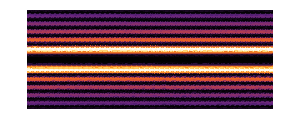

```mathematica
plot1=DensityPlot[IntensityB[L,x,y,0]//.PlotSimpRule//.LSimp,{x,-rplot,rplot},{y,-rplot,rplot},ImageSize->120];
plot2=DensityPlot[IntensityB[L,x,0,z]//.PlotSimpRule//.LSimp,{z,-zplot,zplot},{x,-rplot,rplot},ImageSize->300,AspectRatio->Automatic];
GraphicsRow[{plot1,plot2},Background->Black,Spacings->0,Alignment->{Center,Center}]
 Export["B3_Intensity.jpg",%,"JPEG"];
```

```mathematica
DensityPlot[IntensityB[L,x,y,0]//.PlotSimpRule//.LSimp,{x,-3rplot,3rplot},{y,-3rplot,3rplot},ImageSize->180]
```

-Graphics-

```mathematica
(**************************************************************)
plot1=DensityPlot[PhaseB[L,x,y,0]//.PlotSimpRule//.LSimp,{x,-rplot,rplot},{y,-rplot,rplot},ImageSize->120];
plot2=DensityPlot[PhaseB[L,x,0,z]//.PlotSimpRule//.LSimp,{z,-zplot,zplot},{x,-rplot,rplot},ImageSize->300,AspectRatio->Automatic];
GraphicsRow[{plot1,plot2},Background->Black,Spacings->0,Alignment->{Center,Center}]
 Export["B3_Phase.jpg",%,"JPEG"];
```

#### More Plots for uB

```mathematica
GraphicsRow[ParallelTable[DensityPlot[Evaluate[IntensityB[L,x,y,0]]//.PlotSimpRule,{x,-3rplot,3rplot},{y,-3rplot,3rplot},Mesh->None,PlotPoints->50,ColorFunction->"SunsetColors",PlotRange->All,Frame->False,ImageSize->180 {1,1},PlotRangePadding->0],{L,0,3}],Spacings->0,Background->Black]
```

-Graphics-

```mathematica
Export["/home/eunnie12/Work/1_OptTorque_v14/Math/Bessel_a001_ExiILPhi/uB_table_Intensity_overview.jpg",%,"JPEG"]
```

/home/eunnie12/Work/1_OptTorque_v14/Math/Bessel_a001_ExiILPhi/uB_table_Intensity_overview.jpg

```mathematica
GraphicsRow[ParallelTable[DensityPlot[Evaluate[IntensityB[L,x,y,0]]//.PlotSimpRule,{x,-rplot,rplot},{y,-rplot,rplot},Mesh->None,PlotPoints->50,ColorFunction->"SunsetColors",PlotRange->All,Frame->False,ImageSize->180 {1,1},PlotRangePadding->0],{L,0,3}],Spacings->0,Background->Black]
Export["uB_table_Intensity.jpg",%,"JPEG"];
GraphicsRow[ParallelTable[DensityPlot[Evaluate[PhaseB[L,x,y,0]]//.PlotSimpRule,{x,-rplot,rplot},{y,-rplot,rplot},Mesh->None,PlotPoints->50,ColorFunction->"SunsetColors",PlotRange->All,Frame->False,ImageSize->180 {1,1},PlotRangePadding->0],{L,0,3}],Spacings->0,Background->Black]
Export["uB_table_Phase.jpg",%,"JPEG"];
```

-Graphics-

-Graphics-

### Plots for Vector Fields M, N

#### Evaluate M,N

```mathematica
(**************************************************************)
Mveceval[L_,x0_,y0_,z0_]:=Assuming[A0,Simplify[ReleaseHold[ReleaseHold[Mvec[L,x,y,z]]]//.{x->x0,y->y0,z->z0}]];
(**************************************************************)
Nveceval[L_,x0_,y0_,z0_]:=
Assuming[A0,
Simplify[ReleaseHold[ReleaseHold[Nvec[L,x,y,z]]]//.{x->x0,y->y0,z->z0}]];
(**************************************************************)
Clear[L0]
LSimp={L->L0};
(**************************************************************)
```

```mathematica
Nveceval[L,x,y,z][[1]]
```

1.59155×10^-7 ⅇ^((0.+6.28223×10^6 ⅈ) z+ⅈ L ArcTan[x,y]) ((6.28223×10^6 L y BesselJ[L,109668. √(x^2+y^2)])/(x^2+y^2)+((0.+3.44479×10^11 ⅈ) x (BesselJ[-1+L,109668. √(x^2+y^2)]-1. BesselJ[1+L,109668. √(x^2+y^2)]))/(√(x^2+y^2)))

#### Plot: 2D (xy), vector plot of Re/Im(M), Re./Im(N)

```mathematica
Clear[Mxy,Nxy]
Mxy[L_]=Simplify[{Re[Mveceval[L,x,y,0][[1]]],Re[Mveceval[L,x,y,0][[2]]]}];
Nxy[L_]=Simplify[{Re[Nveceval[L,x,y,0][[1]]],Re[Nveceval[L,x,y,0][[2]]]}];
Clear[MxyIm,NxyIm]
MxyIm[L_]=Simplify[{Im[Mveceval[L,x,y,0][[1]]],Im[Mveceval[L,x,y,0][[2]]]}];
NxyIm[L_]=Simplify[{Im[Nveceval[L,x,y,0][[1]]],Im[Nveceval[L,x,y,0][[2]]]}];
```

```mathematica
Print["M Vector on xy, a=(0,0,1)"]
GraphicsRow[ParallelTable[VectorPlot[Evaluate[Mxy[L0]],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->250 {1,1},VectorStyle->{Red},Mesh->None ,PlotLabel->Real[Subscript[M, L=L0]]],{L0,0,2}],Spacings->0]
 Export["MxyRe_table_L0-2.jpg",%,"JPEG"]; 
GraphicsRow[ParallelTable[VectorPlot[Evaluate[MxyIm[L0]],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->250 {1,1},VectorStyle->{Red},Mesh->None ,PlotLabel->Imag[Subscript[M, L=L0]]],{L0,0,2}],Spacings->0]
 Export["MxyIm_table_L0-2.jpg",%,"JPEG"];
```

M Vector on xy, a=(0,0,1)

-Graphics-

-Graphics-

```mathematica
Print["N Vector on xy, a=(0,0,1)"]
GraphicsRow[ParallelTable[VectorPlot[Evaluate[Nxy[L0]],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->250 {1,1},VectorStyle->{Blue},Mesh->None ,PlotLabel->Real[Subscript[N, L=L0]]],{L0,0,2}],Spacings->0]
 Export["NxyRe_table_L0-2.jpg",%,"JPEG"]; 
GraphicsRow[ParallelTable[VectorPlot[Evaluate[NxyIm[L0]],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->250 {1,1},VectorStyle->{Blue},Mesh->None ,PlotLabel->Imag[Subscript[N, L=L0]]],{L0,0,2}],Spacings->0]
 Export["NxyIm_table_L0-2.jpg",%,"JPEG"];
```

N Vector on xy, a=(0,0,1)

-Graphics-

-Graphics-

```mathematica
GraphicsRow[ParallelTable[VectorPlot[Evaluate[Mxy[L0]],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->200 {1,1},VectorStyle->{Red},Mesh->None ,PlotLabel->Real[Subscript[M, L=L0]]],{L0,0,3}],Spacings->0]
 Export["MxyRe_center_L0-3.jpg",%,"JPEG"]; 
GraphicsRow[ParallelTable[VectorPlot[Evaluate[NxyIm[L0]],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->200 {1,1},VectorStyle->{Blue},Mesh->None ,PlotLabel->Imag[Subscript[N, L=L0]]],{L0,0,3}],Spacings->0]
 Export["NxyIm_center_L0-3.jpg",%,"JPEG"];
```

-Graphics-

-Graphics-

```mathematica
GraphicsRow[ParallelTable[VectorPlot[Evaluate[Mxy[L0]],{x,-rplot,rplot},{y,-rplot,rplot},Frame->False,ImageSize->200 {1,1},VectorStyle->{Red},Mesh->None ,PlotLabel->Real[Subscript[M, L=L0]]],{L0,0,3}],Spacings->0]
 Export["MxyRe_overview_L0-3.jpg",%,"JPEG"]; 
GraphicsRow[ParallelTable[VectorPlot[Evaluate[NxyIm[L0]],{x,-rplot,rplot},{y,-rplot,rplot},Frame->False,ImageSize->200 {1,1},VectorStyle->{Blue},Mesh->None ,PlotLabel->Imag[Subscript[N, L=L0]]],{L0,0,3}],Spacings->0]
 Export["NxyIm_overview_L0-3.jpg",%,"JPEG"];
```

-Graphics-

-Graphics-

#### Plot: Amplitude of M, N

```mathematica
Clear[L0]
LSimp={L->L0};
Clear[MI,NI]
MI[L_]=Norm[Mveceval[L,x,y,z],2];
NI[L_]=Norm[Nveceval[L,x,y,z],2];
```

```mathematica
NormTest=Norm[NvecFull]
```

√(3.66402×10^6 ⅇ^(-2 Im[6.28223×10^6 z+L ArcTan[x,y]]) Abs[BesselJ[L,109668. √(x^2+y^2)]]^2+0.999695 ⅇ^(-2 Im[6.28223×10^6 z+L ArcTan[x,y]]) Abs[(109668. x BesselJ[-1+L,109668. √(x^2+y^2)])/(√(x^2+y^2))-(L BesselJ[L,109668. √(x^2+y^2)])/(x-ⅈ y)]^2+0.999695 ⅇ^(-2 Im[6.28223×10^6 z+L ArcTan[x,y]]) Abs[((0.+109668. ⅈ) y BesselJ[-1+L,109668. √(x^2+y^2)])/(√(x^2+y^2))-(L BesselJ[L,109668. √(x^2+y^2)])/(x-ⅈ y)]^2)

```mathematica
NormTest=Assuming[A0,FullSimplify[NormTest/.L->0/.y->0]]
```

√(3.66402×10^6 BesselJ[0,109668. x]^2+1.20234×10^10 BesselJ[1,109668. x]^2)

```mathematica
NormTest/.x->0
```

1914.16

```mathematica
NormTest2=Assuming[A0,FullSimplify[NI[0]/.y->0]]
```

1. √(1.20234×10^10 BesselJ[1,109668. Abs[x]]^2+(0.0174542 BesselJ[1,109668. Abs[x]]+Abs[x] (957.081 BesselJ[0,109668. Abs[x]]-957.081 BesselJ[2,109668. Abs[x]]))^2/x^2)

```mathematica
Limit[NormTest2,x->0]
```

1914.16

```mathematica
Plot[{NormTest,NormTest2},{x,-rplot,rplot},Ticks->None,ImageSize->200{1,1},Filling->Bottom, PlotRange->All]
```

-Graphics-

```mathematica
(**************************************************************)
Print["|M| on xy, a=(0,0,1)"]
GraphicsRow[ParallelTable[DensityPlot[Evaluate[MI[L0]//.z->0],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->200 {1,1},ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Intensity(M[L0])],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["Mintensity_center_xy_L0-3.jpg",%,"JPEG"];
GraphicsRow[ParallelTable[DensityPlot[Evaluate[MI[L0]//.z->0],{x,-rplot,rplot},{y,-rplot,rplot},Frame->False,ImageSize->200{1,1},PlotPoints->80,ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Intensity(M[L0])],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["Mintensity_overview_xy_L0-3.jpg",%,"JPEG"];
```

|M| on xy, a=(0,0,1)

-Graphics-

-Graphics-

```mathematica
GraphicsRow[ParallelTable[Plot[Evaluate[MI[L0]//.z->0//.y->0],{x,-rplot,rplot},Ticks->None,ImageSize->200{1,1},Filling->Bottom, PlotRange->All,PlotStyle->{Red},PlotLabel->Intensity(Subscript[M, L=L0])],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["Mintensity_x_L0-3.jpg",%,"JPEG"];
GraphicsRow[ParallelTable[Plot[Evaluate[NI[L0]//.z->0//.y->0],{x,-rplot,rplot},Ticks->None,ImageSize->200{1,1},Filling->Bottom, PlotRange->All,PlotLabel->Intensity(Subscript[N, L=L0])],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["Nintensity_x_L0-3.jpg",%,"JPEG"];
```

-Graphics-

-Graphics-

```mathematica
(*Show overlap of M and N *)
GraphicsRow[ParallelTable[Plot[{Evaluate[MI[L0]//.z->0//.y->0],Evaluate[NI[L0]//.z->0//.y->0]},{x,-rplot/50,rplot/50},Ticks->None,ImageSize->200{1,1},Filling->Bottom, PlotRange->All,PlotStyle->{Red,Blue}],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
GraphicsRow[ParallelTable[Plot[{Evaluate[MI[L0]//.z->0//.y->0],Evaluate[NI[L0]//.z->0//.y->0]},{x,-rplot,rplot},Ticks->None,ImageSize->200{1,1},Filling->Bottom, PlotRange->All,PlotStyle->{Red,Blue}],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
```

```mathematica
(**************************************************************)
Print["|N| on xy, a=(0,0,1)"]
GraphicsRow[ParallelTable[DensityPlot[Evaluate[NI[L0]//.z->0],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->200 {1,1},ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Intensity(Subscript[N, L=L0])],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["Nintensity_center_xy_L0-3.jpg",%,"JPEG"];
GraphicsRow[ParallelTable[DensityPlot[Evaluate[NI[L0]//.z->0],{x,-rplot,rplot},{y,-rplot,rplot},Frame->False,ImageSize->200{1,1},PlotPoints->60,ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Intensity(Subscript[N, L=L0])],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["Nintensity_overview_xy_L0-3.jpg",%,"JPEG"];
```

|N| on xy, a=(0,0,1)

-Graphics-

-Graphics-

#### Plot: Phase of M, N

```mathematica
Mveceval[L,x,y,z][[3]]
```

0

```mathematica
Clear[NzRe, NzIm, NzArg]
NzRe[L_]= Re[Nveceval[L,x,y,z][[3]]];
NzIm[L_]= Im[Nveceval[L,x,y,z][[3]]];
NzArg[L_]=Arg[Nveceval[L,x,y,z][[3]]];
```

```mathematica
(**************************************************************)
Print["Nz on xy, a=(0,0,1)"]
GraphicsRow[ParallelTable[DensityPlot[Evaluate[NzRe[L0]//.z->0],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->200 {1,1},ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Real[Nz[L0]]],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["NzRe_center_xy_L0-3.jpg",%,"JPEG"];
GraphicsRow[ParallelTable[DensityPlot[Evaluate[NzRe[L0]//.z->0],{x,-rplot,rplot},{y,-rplot,rplot},Frame->False,ImageSize->200{1,1},PlotPoints->60,ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Real[Nz[L0]]],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["NzRe_overview_xy_L0-3.jpg",%,"JPEG"];
(**************************************************************)
```

Nz on xy, a=(0,0,1)

-Graphics-

-Graphics-

```mathematica
(**************************************************************)
GraphicsRow[ParallelTable[DensityPlot[Evaluate[NzIm[L0]//.z->0],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->200 {1,1},ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Imag[Nz[L0]]],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["NzIm_center_xy_L0-3.jpg",%,"JPEG"];
GraphicsRow[ParallelTable[DensityPlot[Evaluate[NzIm[L0]//.z->0],{x,-rplot,rplot},{y,-rplot,rplot},Frame->False,ImageSize->200{1,1},PlotPoints->60,ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Imag[Nz[L0]]],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["NzIm_overview_xy_L0-3.jpg",%,"JPEG"];
(**************************************************************)
```

-Graphics-

-Graphics-

```mathematica
(**************************************************************)
Print["Nz on xy, a=(0,0,1)"]
GraphicsRow[ParallelTable[DensityPlot[Evaluate[NzArg[L0]//.z->0],{x,-rplot/3,rplot/3},{y,-rplot/3,rplot/3},Frame->False,ImageSize->200 {1,1},PlotPoints->70,ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Arg[Nz[L0]]],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["NzArg_center_xy_L0-3.jpg",%,"JPEG"];
GraphicsRow[ParallelTable[DensityPlot[Evaluate[NzArg[L0]//.z->0],{x,-rplot,rplot},{y,-rplot,rplot},Frame->False,ImageSize->200{1,1},PlotPoints->70,ColorFunction->"SunsetColors",PlotRange->All,PlotLabel->Arg[Nz[L0]]],{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["NzArg_overview_xy_L0-3.jpg",%,"JPEG"];
(**************************************************************)
```

Nz on xy, a=(0,0,1)

-Graphics-

-Graphics-

### Clear variables and free memory

```mathematica
Clear[λ,k,kt,kz,aIn,L,L0,rplot,zplot] 
Clear[plot1, plot2,Mxy,Nxy,MI,NI,MxyIm,NxyIm,NzRe,NzIm,NzArg]
```

## Output using CForm

#### Bessel Function

```mathematica
Series[BesselJ[0,x],{x,0,10}]
Series[BesselJ[-1,x],{x,0,10}]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+O[x]^11

-x/2+x^3/16-x^5/384+x^7/18432-x^9/1474560+O[x]^11

```mathematica
D[BesselJ[L,x],x]
FullSimplify[D[D[BesselJ[L,x],x],x]]
```

1/2 (BesselJ[-1+L,x]-BesselJ[1+L,x])

1/4 (BesselJ[-2+L,x]-2 BesselJ[L,x]+BesselJ[2+L,x])

```mathematica
Plot[Evaluate[Table[BesselJ[L,x],{L,0,4}]],{x,0,5},AspectRatio->Automatic,ImageSize->500]
```

-Graphics-

### CFormRule1

```mathematica
(**************************************************************)
Clear[CFormRule1]
CFormRule1={
ArcTan[x,y]->Phi,
L-> LL,
Sqrt[x^2+y^2]->r,
1/Sqrt[x^2+y^2]->1/r,
BesselJ[LL,kt r]-> BesP,
BesselJ[-1+LL,kt r]->BesPm1
};
(**************************************************************)
```

### Output C Form: 1. Nonsingular

```mathematica
Clear[MvecC,NvecC]
MvecC=Assuming[A0,FullSimplify[MvecFull//.CFormRule1]];
NvecC=Assuming[A0,FullSimplify[NvecFull//.CFormRule1]];
```

```mathematica
MvecFull
NvecFull
```

{ⅇ^(ⅈ (kz z+L ArcTan[x,y])) ((kt y BesselJ[-1+L,kt √(x^2+y^2)])/(√(x^2+y^2))-(L BesselJ[L,kt √(x^2+y^2)])/(ⅈ x+y)),ⅇ^(ⅈ (kz z+L ArcTan[x,y])) (-(kt x BesselJ[-1+L,kt √(x^2+y^2)])/(√(x^2+y^2))+(L BesselJ[L,kt √(x^2+y^2)])/(x-ⅈ y)),0}

{(ⅈ ⅇ^(ⅈ (kz z+L ArcTan[x,y])) kz ((kt x BesselJ[-1+L,kt √(x^2+y^2)])/(√(x^2+y^2))-(L BesselJ[L,kt √(x^2+y^2)])/(x-ⅈ y)))/k,(ⅇ^(ⅈ (kz z+L ArcTan[x,y])) kz ((ⅈ kt y BesselJ[-1+L,kt √(x^2+y^2)])/(√(x^2+y^2))-(L BesselJ[L,kt √(x^2+y^2)])/(x-ⅈ y)))/k,(ⅇ^(ⅈ (kz z+L ArcTan[x,y])) kt^2 BesselJ[L,kt √(x^2+y^2)])/k}

```mathematica
MvecC
NvecC
```

{ⅇ^(ⅈ (LL Phi+kz z)) ((BesPm1 kt y)/r-(BesP LL)/(ⅈ x+y)),ⅇ^(ⅈ (LL Phi+kz z)) (-(BesPm1 kt x)/r+(BesP LL)/(x-ⅈ y)),0}

{(ⅈ ⅇ^(ⅈ (LL Phi+kz z)) kz ((BesPm1 kt x)/r-(BesP LL)/(x-ⅈ y)))/k,(ⅇ^(ⅈ (LL Phi+kz z)) kz (-(BesP LL)/(x-ⅈ y)+(ⅈ BesPm1 kt y)/r))/k,(BesP ⅇ^(ⅈ (LL Phi+kz z)) kt^2)/k}

### Output C Form: 2. Singular (at x=y=0)

```mathematica
(*Approacing from the positive x axis*)
Clear[MvecCr0L0,MvecCr0L1,NvecCr0L0,NvecCr0L1,MvecCr0,NvecCr0]
MvecCr0L0=Limit[Evaluate[MvecFull//.L->0//.{x-> r Cos[Phi],y->r Sin[Phi]}],r->0]
MvecCr0L1=FullSimplify[Limit[Evaluate[MvecFull//.L->1//.{x-> r Cos[Phi],y->r Sin[Phi]}],r->0]]
MvecCr0=Assuming[{A0,L>1},Limit[Evaluate[MvecFull//.{x-> r Cos[Phi],y->r Sin[Phi]}],r->0]]
NvecCr0L0=Limit[Evaluate[NvecFull//.L->0//.{x-> r Cos[Phi],y->r Sin[Phi]}],r->0]
NvecCr0L1=FullSimplify[Limit[Evaluate[NvecFull//.L->1//.{x-> r Cos[Phi],y->r Sin[Phi]}],r->0]]
NvecCr0=Assuming[{A0,L>1},Limit[Evaluate[NvecFull//.{x-> r Cos[Phi],y->r Sin[Phi]}],r->0]]
(**************************************************************)
(* (*Unnecessary to enforce CFormRule*)
MvecCr0L0=MvecCr0L0//.CFormRule1
MvecCr0L1=MvecCr0L1//.CFormRule1
MvecCr0=MvecCr0//.CFormRule1
NvecCr0L0=NvecCr0L0//.CFormRule1
NvecCr0L1=NvecCr0L1//.CFormRule1
NvecCr0=NvecCr0//.CFormRule1 *)
```

{0,0,0}

{1/2 ⅈ ⅇ^(ⅈ kz z) kt,-1/2 ⅇ^(ⅈ kz z) kt,0}

{0,0,0}

{0,0,(ⅇ^(ⅈ kz z) kt^2)/k}

{(ⅈ ⅇ^(ⅈ kz z) kt kz)/(2 k),-(ⅇ^(ⅈ kz z) kt kz)/(2 k),0}

```mathematica
Norm[NvecCr0L0]
Norm[MvecCr0L0]
```

```mathematica
Abs[kt^2/k]
```

0

### Write Output File

```mathematica
file=NotebookDirectory[]<>"CFormList_BesselMN_20150416.txt";
str=OpenWrite[file]
WriteString[str,
"//////////////////////////////////////////////////////////////////\n"<>
"/// For Normal Cases \n"<>
"M[0]="<>ToString[CForm[MvecC[[1]]]]<>";\n"<>
"M[1]="<>ToString[CForm[MvecC[[2]]]]<>";\n"<>
"M[2]="<>ToString[CForm[MvecC[[3]]]]<>";\n"<>
"N[0]="<>ToString[CForm[NvecC[[1]]]]<>";\n"<>
"N[1]="<>ToString[CForm[NvecC[[2]]]]<>";\n"<>
"N[2]="<>ToString[CForm[NvecC[[3]]]]<>";\n"<>
"//////////////////////////////////////////////////////////////////\n"];
Close[str];
```

OutputStream[…]

```mathematica
str=OpenAppend[file]
WriteString[str,"//////////////////////////////////////////////////////////////////\n"<>
"//////////////////////////////////////////////////////////////////\n"<>
"/// For L=1, r=0 \n"<>
"M[0]="<>ToString[CForm[MvecCr0L1[[1]]]]<>";\n"<>
"M[1]="<>ToString[CForm[MvecCr0L1[[2]]]]<>";\n"<>
"M[2]="<>ToString[CForm[MvecCr0L1[[3]]]]<>";\n"<>
"N[0]="<>ToString[CForm[NvecCr0L1[[1]]]]<>";\n"<>
"N[1]="<>ToString[CForm[NvecCr0L1[[2]]]]<>";\n"<>
"N[2]="<>ToString[CForm[NvecCr0L1[[3]]]]<>";\n"<>
"//////////////////////////////////////////////////////////////////\n"<>
"/// For L=0, r=0 \n"<>
"M[0]="<>ToString[CForm[MvecCr0L0[[1]]]]<>";\n"<>
"M[1]="<>ToString[CForm[MvecCr0L0[[2]]]]<>";\n"<>
"M[2]="<>ToString[CForm[MvecCr0L0[[3]]]]<>";\n"<>
"N[0]="<>ToString[CForm[NvecCr0L0[[1]]]]<>";\n"<>
"N[1]="<>ToString[CForm[NvecCr0L0[[2]]]]<>";\n"<>
"N[2]="<>ToString[CForm[NvecCr0L0[[3]]]]<>";\n"<>
"//////////////////////////////////////////////////////////////////\n"<>
"/// For L>1, r=0 \n"<>
"M[0]="<>ToString[CForm[MvecCr0[[1]]]]<>";\n"<>
"M[1]="<>ToString[CForm[MvecCr0[[2]]]]<>";\n"<>
"M[2]="<>ToString[CForm[MvecCr0[[3]]]]<>";\n"<>
"N[0]="<>ToString[CForm[NvecCr0[[1]]]]<>";\n"<>
"N[1]="<>ToString[CForm[NvecCr0[[2]]]]<>";\n"<>
"N[2]="<>ToString[CForm[NvecCr0[[3]]]]<>";\n"<>
"//////////////////////////////////////////////////////////////////\n"];
Close[str];
FilePrint[%]
```

OutputStream[…]

//////////////////////////////////////////////////////////////////
/// For Normal Cases 
M[0]=Power(E,I*(LL*Phi + kz*z))*((BesPm1*kt*y)/r - (BesP*LL)/(Complex(0,1)*x + y));
M[1]=Power(E,I*(LL*Phi + kz*z))*(-((BesPm1*kt*x)/r) + (BesP*LL)/(x - Complex(0,1)*y));
M[2]=0;
N[0]=(Complex(0,1)*Power(E,I*(LL*Phi + kz*z))*kz*((BesPm1*kt*x)/r - (BesP*LL)/(x - Complex(0,1)*y)))/k;
N[1]=(Power(E,I*(LL*Phi + kz*z))*kz*(-((BesP*LL)/(x - Complex(0,1)*y)) + (Complex(0,1)*BesPm1*kt*y)/r))/k;
N[2]=(BesP*Power(E,I*(LL*Phi + kz*z))*Power(kt,2))/k;
//////////////////////////////////////////////////////////////////
//////////////////////////////////////////////////////////////////
//////////////////////////////////////////////////////////////////
/// For L=1, r=0 
M[0]=Complex(0,0.5)*Power(E,I*kz*z)*kt;
M[1]=-(Power(E,I*kz*z)*kt)/2.;
M[2]=0;
N[0]=(Complex(0,0.5)*Power(E,I*kz*z)*kt*kz)/k;
N[1]=-(Power(E,I*kz*z)*kt*kz)/(2.*k);
N[2]=0;
//////////////////////////////////////////////////////////////////
/// For L=0, r=0 
M[0]=0;
M[1]=0;
M[2]=0;
N[0]=0;
N[1]=0;
N[2]=(Power(E,I*kz*z)*Power(kt,2))/k;
//////////////////////////////////////////////////////////////////
/// For L>1, r=0 
M[0]=0;
M[1]=0;
M[2]=0;
N[0]=0;
N[1]=0;
N[2]=0;
//////////////////////////////////////////////////////////////////